```mathematica
Total[Table[newAssoc[key]["colofour"],{key,{36166,31738,29608,36112,31714}}]]
```

b01/2+b02/2+b03/2+b04/2+b05/2-b06/2-b07/2-b08/2-b09/2-b10/2-b11/3-b12/3-b13/3-b14/3-b15/3-b16/3-b17/3-b18/3-b19/3-b20/3+(2 b21)/3+(2 b22)/3+(2 b23)/3+(2 b24)/3+(2 b25)/3-b26/2-b27/2-b28/2-b29/2-b30/2+b31/2+b32/2+b33/2+b34/2+b35/2-(5 b36)/12-(5 b37)/12-(5 b38)/12-(5 b39)/12-(5 b40)/12+(7 b41)/12+(7 b42)/12+(7 b43)/12+(7 b44)/12+(7 b45)/12-b46/4-b47/4-b48/4-b49/4-b50/4

```mathematica
Table[{key->newAssoc[key]["colofour"]},{key,{36166,31738,29608,36112,31714}}]
```

{{36166→b01/3-b03/6+b05/3-b07/6-b08/6-b09/6+b11/6-b12/3-b14/3+b15/6-b16/3+b17/6+b19/6-b20/3+b21/6+b22/6+b24/6+b25/6-b26/3+b28/6-b30/3+b32/6+b33/6+b34/6-b36/12-b37/12-b38/12-b39/12-b40/12+(5 b41)/12-b42/12-b43/12-b44/12+(5 b45)/12-b46/12-b47/12+b48/12-b49/12-b50/12},{31738→b02/3+b03/3-b05/6-b06/6-b09/6-b10/6-b11/3+b12/6+b13/6-b14/3+b16/6-b17/3-b18/3+b19/6+b21/6+b22/6+b23/6+b24/6-b27/3-b28/3+b30/6+b31/6+b34/6+b35/6-b36/12-b37/12-b38/12-b39/12-b40/12-b41/12+(5 b42)/12+(5 b43)/12-b44/12-b45/12-b46/12-b47/12-b48/12-b49/12+b50/12},{29608→-b02/6+b04/3+b05/3-b06/6-b07/6-b08/6-b11/3-b13/3+b14/6+b15/6+b16/6+b18/6-b19/3-b20/3+b21/6+b23/6+b24/6+b25/6+b27/6-b29/3-b30/3+b31/6+b32/6+b33/6-b36/12-b37/12-b38/12-b39/12-b40/12-b41/12-b42/12-b43/12+(5 b44)/12+(5 b45)/12-b46/12+b47/12-b48/12-b49/12-b50/12},{36112→b01/3+b02/3-b04/6-b08/6-b09/6-b10/6+b11/6+b12/6-b13/3-b15/3-b16/3-b17/3+b18/6+b20/6+b21/6+b22/6+b23/6+b25/6-b26/3-b27/3+b29/6+b33/6+b34/6+b35/6-b36/12-b37/12-b38/12-b39/12-b40/12+(5 b41)/12+(5 b42)/12-b43/12-b44/12-b45/12-b46/12-b47/12-b48/12+b49/12-b50/12},{31714→-b01/6+b03/3+b04/3-b06/6-b07/6-b10/6-b12/3+b13/6+b14/6-b15/3+b17/6-b18/3-b19/3+b20/6+b22/6+b23/6+b24/6+b25/6+b26/6-b28/3-b29/3+b31/6+b32/6+b35/6-b36/12-b37/12-b38/12-b39/12-b40/12-b41/12-b42/12+(5 b43)/12+(5 b44)/12-b45/12+b46/12-b47/12-b48/12-b49/12-b50/12}}

```mathematica
CompVector[v1_,v2_]:=Block[{result,i},
result=Range[Length[v1]];
For[i=1,i≤Length[v1],i++,
If[v1[[i]]==v2[[i]],result[[i]]=v1[[i]],result[[i]]=0]
];
result
]
```

```mathematica
t1=CompVector[CoeffVector[newAssoc[36166]["colofour"]],CoeffVector[newAssoc[31738]["colofour"]]]
```

{0,0,0,0,0,0,0,0,-1/6,0,0,0,0,-1/3,0,0,0,0,1/6,0,1/6,1/6,0,1/6,0,0,0,0,0,0,0,0,0,1/6,0,-1/12,-1/12,-1/12,-1/12,-1/12,0,0,0,-1/12,0,-1/12,-1/12,0,-1/12,0,0}

```mathematica
t2=CompVector[t1,CoeffVector[newAssoc[29608]["colofour"]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/6,0,0,1/6,0,0,0,0,0,0,0,0,0,0,0,-1/12,-1/12,-1/12,-1/12,-1/12,0,0,0,0,0,-1/12,0,0,-1/12,0,0}

```mathematica
t3=CompVector[t2,CoeffVector[newAssoc[36112]["colofour"]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/12,-1/12,-1/12,-1/12,-1/12,0,0,0,0,0,-1/12,0,0,0,0,0}

```mathematica
t4=CompVector[t3,CoeffVector[newAssoc[31714]["colofour"]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/12,-1/12,-1/12,-1/12,-1/12,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
t4*myVars//Total
```

-b36/12-b37/12-b38/12-b39/12-b40/12

```mathematica
CoeffToFormula[vect
```

```mathematica
CoeffVector[exp_]:=Table[Coefficient[ exp,v,1],{v,Sort[myVars,SymbolComp2]}]
```

```mathematica
CoeffVector[newAssoc[36166]["colofour"]]+CoeffVector[newAssoc[31738]["colofour"]]+CoeffVector[newAssoc[29608]["colofour"]]+CoeffVector[newAssoc[36112]["colofour"]]-+CoeffVector[newAssoc[31714]["colofour"]]-5*CoeffVector[newAssoc[31714]["colofour"]]
```

{5/3,1/2,-11/6,-11/6,1/2,2/3,2/3,-1/2,-1/2,2/3,-1/3,2,-3/2,-3/2,2,-1/3,-3/2,2,2,-3/2,2/3,-1/2,-1/2,-1/2,-1/2,-5/3,-1/2,11/6,11/6,-1/2,-2/3,-2/3,1/2,1/2,-2/3,1/6,1/6,1/6,1/6,1/6,7/6,7/6,-7/3,-7/3,7/6,-5/6,1/3,1/3,1/3,1/3,0}

```mathematica
Table[{key->CoeffVector[newAssoc[key]["colofour"]]},{key,{36166,31738,29608,36112,31714}}]
```

{{36166→{1/3,0,-1/6,0,1/3,0,-1/6,-1/6,-1/6,0,1/6,-1/3,0,-1/3,1/6,-1/3,1/6,0,1/6,-1/3,1/6,1/6,0,1/6,1/6,-1/3,0,1/6,0,-1/3,0,1/6,1/6,1/6,0,-1/12,-1/12,-1/12,-1/12,-1/12,5/12,-1/12,-1/12,-1/12,5/12,-1/12,-1/12,1/12,-1/12,-1/12,0}},{31738→{0,1/3,1/3,0,-1/6,-1/6,0,0,-1/6,-1/6,-1/3,1/6,1/6,-1/3,0,1/6,-1/3,-1/3,1/6,0,1/6,1/6,1/6,1/6,0,0,-1/3,-1/3,0,1/6,1/6,0,0,1/6,1/6,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,5/12,5/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,1/12,0}},{29608→{0,-1/6,0,1/3,1/3,-1/6,-1/6,-1/6,0,0,-1/3,0,-1/3,1/6,1/6,1/6,0,1/6,-1/3,-1/3,1/6,0,1/6,1/6,1/6,0,1/6,0,-1/3,-1/3,1/6,1/6,1/6,0,0,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,5/12,5/12,-1/12,1/12,-1/12,-1/12,-1/12,0}},{36112→{1/3,1/3,0,-1/6,0,0,0,-1/6,-1/6,-1/6,1/6,1/6,-1/3,0,-1/3,-1/3,-1/3,1/6,0,1/6,1/6,1/6,1/6,0,1/6,-1/3,-1/3,0,1/6,0,0,0,1/6,1/6,1/6,-1/12,-1/12,-1/12,-1/12,-1/12,5/12,5/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,1/12,-1/12,0}},{31714→{-1/6,0,1/3,1/3,0,-1/6,-1/6,0,0,-1/6,0,-1/3,1/6,1/6,-1/3,0,1/6,-1/3,-1/3,1/6,0,1/6,1/6,1/6,1/6,1/6,0,-1/3,-1/3,0,1/6,1/6,0,0,1/6,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,-1/12,5/12,5/12,-1/12,1/12,-1/12,-1/12,-1/12,-1/12,0}}}

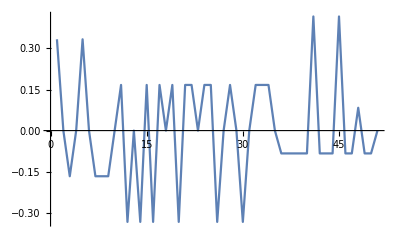
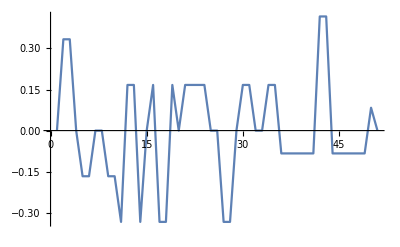
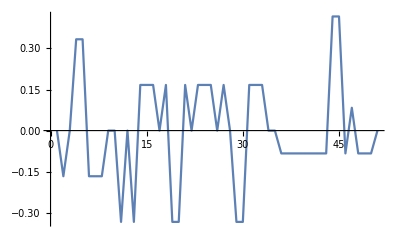
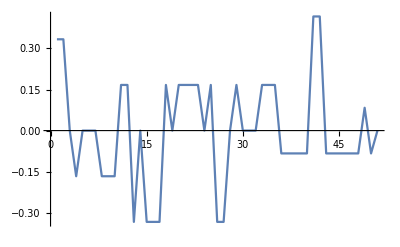
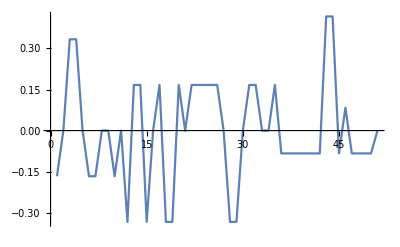
{{36166→-Graphics-},{31738→-Graphics-},{29608→-Graphics-},{36112→-Graphics-},{31714→-Graphics-}}

```mathematica
Table[{key->ListLinePlot[CoeffVector[newAssoc[key]["colofour"]]]},{key,{36166,31738,29608,36112,31714}}]
```